1000

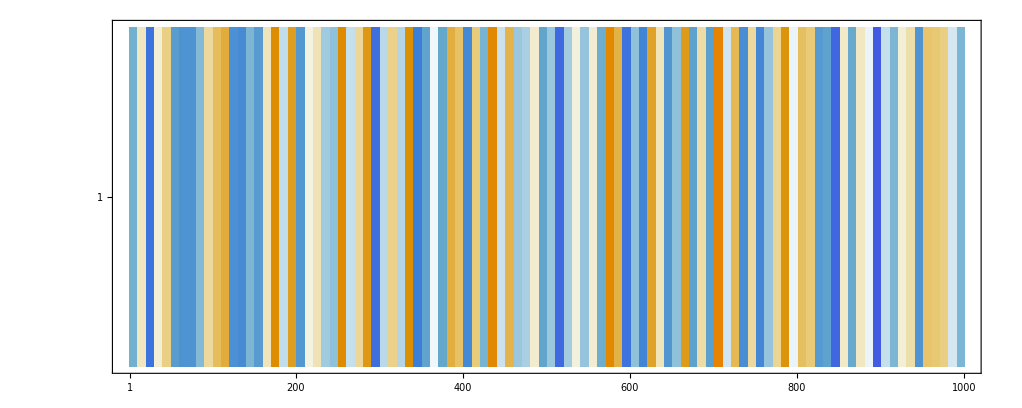

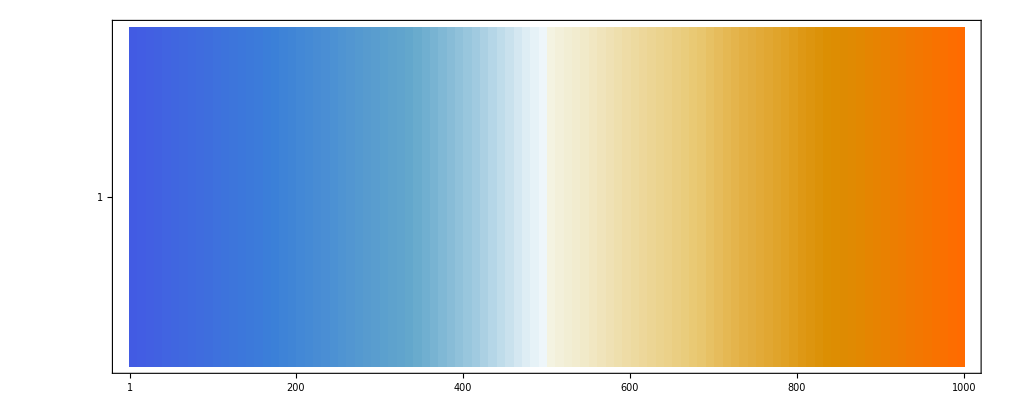

```mathematica
m = Input["N"]
For[n = 1, n≤m, n++, a[n] = RandomInteger[{-100, 100}]]
MatrixPlot[{Array[a, m]}]
For[i = 1, i<m, i++, For[n = 1, n≤m, n++, If[a[n]>a[n+1], temp = a[n]; a[n] = a[n+1]; a[n+1] =temp]]]
MatrixPlot[{Array[a, m]}]
```

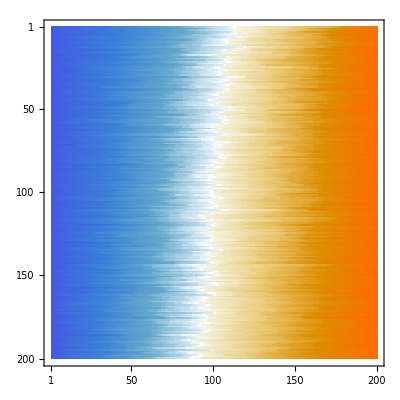

```mathematica
m =Input["N"];
sum1 =0;
sum2 = 0;
For[i = 0, i<m, i++; For[j = 0, j<m, j++; double[i, j] = RandomInteger[{-100, 100}]]];
MatrixPlot[Array[double, {m, m}]];
For[i = 1, i<=m, i++, For[k = 1, k < m, k++,For[j= 1, j≤m, j++, If[double[i, j]>double[i, j+1], temp = double[i, j]; double[i, j] = double[i, j+1]; double[i, j+1] =temp]]]]
MatrixPlot[Array[double, {m, m}]];
For[k = 1, k <m, k++, For[i = 1, i<m, i++, For[j= 1, j≤m, j++, sum1+=double[i,j]; ]; i++;For[j= 1, j≤m, j++, sum2+=double[i,j]; ]; i-- ;If[sum1 > sum2, For[j = 1, j≤m, j++, temp = double[i, j]; double[i, j] = double[i+1, j]; double[i+1, j] = temp]]; sum1 = 0; sum2 = 0; ]];
Array[double, {m,m}]//MatrixPlot
```